#### Preamble

```mathematica
ClearAll@@{$Context<>"*"}
SetDirectory[NotebookDirectory[]]
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; 
StartScheduledTask[saveTask] (*Saves nb each 15 minutes*) ;

<<"MaTeX`"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Maxima_Minima.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optics_Mie.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/jet_jet-extended.wls"
```

/home/juanathan/Documentos/MSc_Thesis/3-FEM-Calc/3-Incrusted

#### Plots format

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
colors[[1]] = ColorData[3,2];
PrependTo[colors,Black];
```

```mathematica
fs=9;
cdata3 = Table[ColorData[3,i],{i,10}];cdata3[[3]] = Purple;
texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
```

```mathematica
graphsOpts:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->colors}
graphsOptsDash:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->Table[Directive[Dashed,colors[[i]]],{i,10}]}
```

```mathematica
graphsOptsPolar:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[PointSize[.015],colors[[i]]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
graphsOptsPolarDashed:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[Dashed,PointSize[.015],colors[[i]]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
```

```mathematica
graphsOptsDensity := { BaseStyle -> texStyle, FrameStyle -> Black, PlotRange -> Full,  ColorFunctionScaling -> True, ColorFunction -> JetExtended, Mesh -> None, ImageSize -> 150, PlotRangePadding -> None  }
graphsOptsDensityExport :={PlotLegends->None,FrameTicks->None, BaseStyle -> texStyle, FrameStyle -> Black, PlotRange -> Full,  ColorFunctionScaling -> False, ColorFunction -> JetExtended, Mesh -> None, ImageSize -> 150, PlotRangePadding -> None}
```

#### Sorting Functions

```mathematica
maxPair[list_,ind_]:= SortBy[list, #[[ind]]&][[-1,{1,ind}]]
makePairs[list_,ind_]:=Map[Table[#[[;;,{1,i}]],{i,ind}]&,list]
```

Efficiencies

```mathematica
scaling = "Log"
scaling = None
```

Log

None

### Mie

```mathematica
radius = 12.5;
nNP=JohnsonChristyAuRefSize[#,radius]&;
wlength=Range[400,600,2.5];
max=scaQ=extQ={0,0};

scaFunc[lda_]:=Map[MieScatteringQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
extFunc[lda_]:=Map[MieExtinctionQ[{nMat[#],nNP[#]},#,radius]&,toMap[lda]];
```

```mathematica
i=1;
nMat=1.&;
extQ[[i]]=extFunc[wlength];
scaQ[[i]]=scaFunc[wlength];
max[[i]]=FindExtrema[#,wlength[[{1,-1}]],10.,"Maxima"][[1,1]]&/@{extFunc,scaFunc};

i++;
nMat=1.5&;
extQ[[i]]=extFunc[wlength];
scaQ[[i]]=scaFunc[wlength];
max[[i]]=FindExtrema[#,wlength[[{10,-1}]],10.,"Maxima"][[1,1]]&/@{extFunc,scaFunc};

max=Reverse@Transpose[max];
```

```mathematica
mie=MapThread[Show[{ListPlot[#,DataRange->wlength[[{1,-1}]],Joined->True,Filling->{1->{2}},ScalingFunctions->scaling,PlotStyle->{Directive[Thick,Dashed,Green],Directive[Thick,Dashed,Green]}],
ListPlot[Callout[#,ToString[IntegerPart@#[[1]]],Left]&/@#2,ScalingFunctions->scaling,PlotStyle->Red]},PlotRange->All]&,{{scaQ,extQ-scaQ},max}]
```

{-Graphics-,-Graphics-}

### Interface

```mathematica
cases = {-1,7,6,5,1,2,3,4,-2};
```

```mathematica
data = FileNames["1*csv","Normal"];
data = data[[#]]&/@cases;
 data//TableForm

data =Drop[Import[#,"Data"],5]&/@ data;
maxPoints = Array[maxPair[data[[#1,10;;]],1+#2]&,{Length[data],2}] //Transpose;
data = makePairs[data,{2,3}] // Transpose;
```

Normal/1-Efficiency-Supported-Internal.csv
Normal/1-Efficiencies-p75.csv
Normal/1-Efficiencies-p50.csv
Normal/1-Efficiencies-p25.csv
Normal/1-Efficiencies-00.csv
Normal/1-Efficiencies-m25.csv
Normal/1-Efficiencies-m50.csv
Normal/1-Efficiencies-m75.csv
Normal/1-Efficiency-Embedded-Internal.csv

```mathematica
(*Quitar lo de mie?? Supongo que sí*)
plots = MapThread[Show[{
ListPlot[#1,ImageSize->350,Evaluate[graphsOpts],Joined->True,ScalingFunctions->scaling, Filling->{{1->{5}},{5->{9}}}],
ListPlot[Callout[#,ToString[NumberForm[N[#[[1]]],{4,1}]],Below]&/@#,PlotStyle->Magenta,ScalingFunctions->scaling, Joined->True]& @ #2,#3}]&,{data,maxPoints,mie}]
```

{-Graphics-,-Graphics-}

```mathematica
name = "1-Efficiencies"
legendas = SwatchLegend[colors[[;;9]],NumberForm[#,{3,2}]&/@ Range[1,-1,-.25]];

Export[FileNameJoin[{"Normal",name,"legendas.pdf"}],legendas]
MapIndexed[Export[FileNameJoin[{"Normal",name,name<>ToString[First[#2]]<>".pdf"}],#1]&,plots]
```

1-Efficiencies

Normal/1-Efficiencies/legendas.pdf

{Normal/1-Efficiencies/1-Efficiencies1.pdf,Normal/1-Efficiencies/1-Efficiencies2.pdf}

Near Field Abs

```mathematica
cases = {7,6,5,1,2,3,4};
radius = 12.5;
```

```mathematica
data =  FileNames["2*csv","Normal"];
data = data[[#]]&/@cases;
data//TableForm

data =Drop[Import[#,"Data"],8]&/@ data;
limData = radius*3.5;
lim = radius*3;
```

Normal/2-Near-p75.csv
Normal/2-Near-p50.csv
Normal/2-Near-p25.csv
Normal/2-Near-00.csv
Normal/2-Near-m25.csv
Normal/2-Near-m50.csv
Normal/2-Near-m75.csv

```mathematica
max = Max[data[[;;,;;,4]]] (*To normalize all cases*)
case = ConstantArray[-1,7] (*To place above or below the glass*)

dataX = Table[Select[data[[i]], Abs[#[[2]]]<.001   &],{i,Length[data]}];
dataX = MapThread[#1/. {x_,y_,z_,norm_} -> {-x, #2 * z, norm/max} &,{dataX, case}];
dataX = Table[Select[dataX[[i]], (Abs[#[[1]]]<limData && Abs[#[[2]]]<limData) &],{i,Length[dataX]}];

dataY = Table[Select[data[[i]], Abs[#[[1]]]<.001   &],{i,Length[data]}];
dataY = MapThread[#/. {x_,y_,z_,norm_} -> {y, #2 * z, norm/max} &, {dataY, case}];
dataY = Table[Select[dataY[[i]], (Abs[#[[1]]]<limData && Abs[#[[2]]]<limData) &],{i,Length[dataY]}];
```

6.77159

{-1,-1,-1,-1,-1,-1,-1}

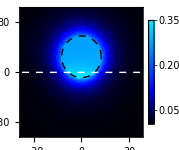
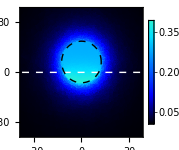
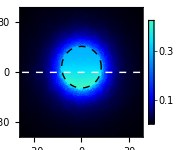
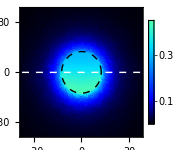
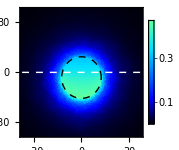
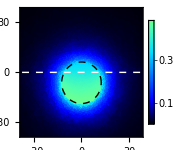
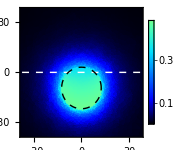

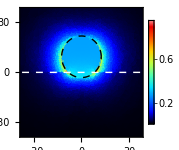

```mathematica
case = Table[i,{i,.75,-.75,-.25}];
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{0,radius*#},radius]}&/@case;

plotsX = MapThread[ListDensityPlot[#1,PlotRange->{{-1,1},{-1,1}}*lim,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}]
plotsY = MapThread[ListDensityPlot[#1,PlotRange->{{-1,1},{-1,1}}*lim,ColorFunctionScaling->False,Evaluate[graphsOptsDensity], Epilog->#2, PlotLegends->Automatic]&, {dataY,system}]
```

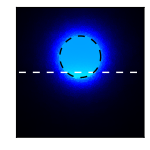
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
case = Table[i,{i,.75,-.75,-.25}];
system = {White,Dashed, Line[{{-lim,0},{lim,0}}],Black, Circle[{0,radius*#},radius]}&/@case;

plotsX = MapThread[ListDensityPlot[#1,PlotRange->{{-1,1},{-1,1}}*lim,ColorFunctionScaling->False,Evaluate[graphsOptsDensityExport], Epilog->#2, PlotLegends->Automatic]&, {dataX,system}]
plotsY = MapThread[ListDensityPlot[#1,PlotRange->{{-1,1},{-1,1}}*lim,ColorFunctionScaling->False,Evaluate[graphsOptsDensityExport], Epilog->#2, PlotLegends->Automatic]&, {dataY,system}]
```

```mathematica
legends = {0,0};
legends[[1]] = Plot[x, {x, 0, max}, BaseStyle -> texStyle, 
  FrameTicks -> {{None, None}, {Automatic, None}},
  FrameStyle -> Black,    Frame-> True,
  AspectRatio -> 1/30, 
  PlotRange -> All, PlotRangePadding -> None, 
 ImageSize -> {60, 25/2}*4]
 
legends[[2]] =  DensityPlot[x, {x, 0,max}, {y, 0, 1}, BaseStyle -> texStyle, 
  FrameTicks -> {{None, None}, {None, None}},
  FrameStyle -> Black, 
  AspectRatio -> 1/30, 
  PlotRange -> All, ColorFunction -> JetExtended, 
  PlotPoints -> 40, PlotRangePadding -> None, 
 ImageSize -> {60, 25/2}*4]
```

-Graphics-

-Graphics-

```mathematica
name = "2-NearY"
MapIndexed[Export[FileNameJoin[{"Normal",name,name<>ToString[First[#2]]<>".svg"}],#1]&,plotsY]
MapIndexed[Export[FileNameJoin[{"Normal",name,"Legend"<>{".pdf",".svg"}[[First[#2]]]}],#1]&,legends]
name = "2-NearX"
MapIndexed[Export[FileNameJoin[{"Normal",name,name<>ToString[First[#2]]<>".svg"}],#1]&,plotsX]
```

2-NearY

{Normal/2-NearY/2-NearY1.svg,Normal/2-NearY/2-NearY2.svg,Normal/2-NearY/2-NearY3.svg,Normal/2-NearY/2-NearY4.svg,Normal/2-NearY/2-NearY5.svg,Normal/2-NearY/2-NearY6.svg,Normal/2-NearY/2-NearY7.svg}

{Normal/2-NearY/Legend.pdf,Normal/2-NearY/Legend.svg}

2-NearX

{Normal/2-NearX/2-NearX1.svg,Normal/2-NearX/2-NearX2.svg,Normal/2-NearX/2-NearX3.svg,Normal/2-NearX/2-NearX4.svg,Normal/2-NearX/2-NearX5.svg,Normal/2-NearX/2-NearX6.svg,Normal/2-NearX/2-NearX7.svg}

Far Field (Normal X, All WaveLengths)

```mathematica
cases = {7,6,5,1,2,3,4};
```

```mathematica
data =  FileNames["3*csv","Normal"]; 
data = data[[#]]&/@cases;
data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
data = Map[Partition[#,51]&,data]; (*Separete eat wlength value*)
```

Normal/3-Abs-FarX-p75.csv
Normal/3-Abs-FarX-p50.csv
Normal/3-Abs-FarX-p25.csv
Normal/3-Abs-FarX-00.csv
Normal/3-Abs-FarX-m25.csv
Normal/3-Abs-FarX-m50.csv
Normal/3-Abs-FarX-m75.csv

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}];

arrows ={Red,Arrow[-#2*{{Cos[#1],Sin[#1]},.025{Cos[#1],Sin[#1]}}]}&;
```

```mathematica
max = Max[#[[;;,;;,2]]]&/@data;
max = Max[max]
case = Table[i,{i,.75,-.75,-.25}];

MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->max*1.65,
PolarAxesOrigin->{{Left,Up},max},
PlotStyle->Directive[PointSize[.015],#3],
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0}, max*1.65,{0,-Pi}],LightYellow,Disk[1*{0,max*#2}/3.5,max /3.5]},
Epilog->arrows[Pi/2,max*1.1]
]&,
{data,case,colors[[2;;Length[data]+1]]}]
```

2.16377

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
aa = 10
prol = MapThread[{Opacity[.25],LightYellow, Disk[1*{0,max*#1/aa},max /aa], Opacity[1],#2, Circle[1*{0,max*#1/aa},max /aa] }&,{Reverse[case],colors[[;;Length[data]]]}];

plots = ListPolarPlot[data/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->max*1.65,
PolarAxesOrigin->{{Left,Up},max},
PlotStyle->Table[Directive[PointSize[.015],colors[[i]]],{i,2,8,1}],
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0}, max*1.65,{0,-Pi}],LightYellow,Disk[1*{0,0}/3.5,max /3.5]},
(*Prolog->{LightBlue,Disk[{0,0}, max*1.65,{0,-Pi}],prol},*)
Epilog->arrows[Pi/2,max*1.1]
]

name = "4-Far-X"
Export[FileNameJoin[{"Normal",name,name<>".pdf"}],plots]
Export[FileNameJoin[{"Normal",name,name<>".svg"}],plots]
```

10

-Graphics-

4-Far-X

Normal/4-Far-X/4-Far-X.pdf

Normal/4-Far-X/4-Far-X.svg

Far Field (Normal Y, All WaveLengths)

```mathematica
cases = {7,6,5,1,2,3,4};
```

```mathematica
data =  FileNames["4*csv","Normal"]; 
data = data[[#]]&/@cases;
data//TableForm
data =Drop[Import[#,"Data"],8]&/@ data;
data = Map[Partition[#,51]&,data]; (*Separete eat wlength value*)
```

Normal/4-Abs-FarY-p75.csv
Normal/4-Abs-FarY-p50.csv
Normal/4-Abs-FarY-p25.csv
Normal/4-Abs-FarY-00.csv
Normal/4-Abs-FarY-m25.csv
Normal/4-Abs-FarY-m50.csv
Normal/4-Abs-FarY-m75.csv

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}];

arrows ={Red,Arrow[-#2*{{Cos[#1],Sin[#1]},.025{Cos[#1],Sin[#1]}}]}&;
```

```mathematica
max = Max[#[[;;,;;,2]]]&/@data;
max = Max[max]
case = Table[i,{i,.75,-.75,-.25}];

MapThread[
ListPolarPlot[#1/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->max*1.65,
PolarAxesOrigin->{{Left,Up},max},
PlotStyle->Directive[PointSize[.015],#3],
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0}, max*1.65,{0,-Pi}],LightYellow,Disk[1*{0,max*#2}/3.5,max /3.5]},
Epilog->arrows[Pi/2,max*1.1]
]&,
{data,case,colors[[2;;Length[data]+1]]}]
```

2.16377

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
aa = 10
prol = MapThread[{Opacity[.25],LightYellow, Disk[1*{0,max*#1/aa},max /aa], Opacity[1],#2, Circle[1*{0,max*#1/aa},max /aa] }&,{Reverse[case],colors[[;;Length[data]]]}];

plots = ListPolarPlot[data/.{theta_,rad_}-> {theta+Pi/2.,rad},PlotRange->max*1.65,
PolarAxesOrigin->{{Left,Up},max},
PlotStyle->Table[Directive[PointSize[.015],colors[[i]]],{i,2,8,1}],
Evaluate[graphsOptsPolar],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0}, max*1.65,{0,-Pi}],LightYellow,Disk[1*{0,0}/3.5,max /3.5]},
(*Prolog->{LightBlue,Disk[{0,0}, max*1.65,{0,-Pi}],prol},*)
Epilog->arrows[Pi/2,max*1.1]
]

name = "5-Far-Y"
Export[FileNameJoin[{"Normal",name,name<>".pdf"}],plots]
Export[FileNameJoin[{"Normal",name,name<>".svg"}],plots]
```

10

-Graphics-

5-Far-Y

Normal/5-Far-Y/5-Far-Y.pdf

Normal/5-Far-Y/5-Far-Y.svg